# Thesis Project: Cement Hydrates

## C-S-H

```mathematica
wrkdir = "/home/pacman/Documents/yachay-physics/Ninth-V2-Semester/thesis-project/project/scripts/week-1/eos/";
SetDirectory[wrkdir]
```

/home/pacman/Documents/yachay-physics/Ninth-V2-Semester/thesis-project/project/scripts/week-1/eos

### The k-point grid

```mathematica
bulk = Import["POSCAR-init", "Table"];
```

```mathematica
lattbulk = bulk[[2, 1]] bulk[[3;;5]]
```

{{13.5354,0.18446,0.00755401},{-16.2629,24.8887,-0.00875423},{0.543338,-0.483321,23.4374}}

```mathematica
{a, b, c} = lattbulk;
```

```mathematica
Δk = Table[0.07-0.005 i, {i, 0, 10}];
```

```mathematica
Δk//Map[{#, Round[((b×c)/((a×b).c)//Norm)/#],
Round[((c×a)/((a×b).c)//Norm)/#],
Round[((a×b)/((a×b).c)//Norm)/#]}&, #]&//TableForm
```

0.07 | 1 | 1 | 1
0.065 | 1 | 1 | 1
0.06 | 1 | 1 | 1
0.055 | 2 | 1 | 1
0.05 | 2 | 1 | 1
0.045 | 2 | 1 | 1
0.04 | 2 | 1 | 1
0.035 | 2 | 1 | 1
0.03 | 3 | 1 | 1
0.025 | 3 | 2 | 2
0.02 | 4 | 2 | 2

We will run the xkp.sh script for k-points (1 1 1), (2 1 1), and (3 1 1).

### Convergency of k-points

```mathematica
wrkdir = "/home/pacman/Documents/yachay-physics/Ninth-V2-Semester/thesis-project/project/scripts/week-1/kpoints/";
SetDirectory[wrkdir]
```

/home/pacman/Documents/yachay-physics/Ninth-V2-Semester/thesis-project/project/scripts/week-1/kpoints

```mathematica
data = Import["kp.dat"]
```

{{1,1,1,-49946.,-49946.,-49946.,-49946.},{2,1,1,-49946.7,-49946.7,-49946.7,-49946.7},{3,1,1,-49946.6,-49946.6,-49946.6,-49946.6}}

```mathematica
kpdat =data[[All,{1,4}]]//Map[#/{1,690}&]
```

{{1,-72.3855},{2,-72.3865},{3,-72.3864}}

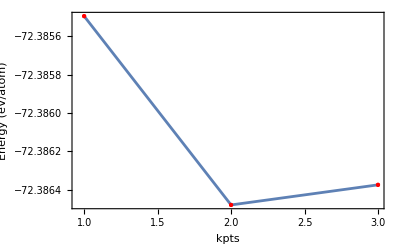

```mathematica
ListPlot[kpdat,
PlotRange->All,
Joined->True,
Mesh->Full,
MeshStyle->
{Directive[PointSize[Medium], Red]},
Frame->True,
FrameLabel->
{"kpts", "Energy (eV/atom)"},
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->18},
ImageSize->400]
```

Let’s analyse the convergency of these data using the 1 meV/atom criteria

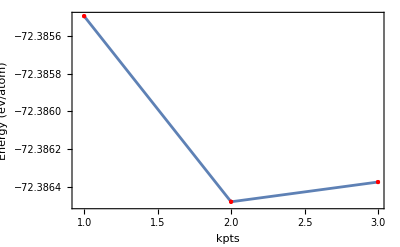

```mathematica
ListPlot[kpdat,
PlotRange->{kpdat[[1,2]], kpdat[[1,2]]-10^-3},
Joined->True,
Mesh->Full,
MeshStyle->
{Directive[PointSize[Medium], Red]},
Frame->True,
FrameLabel->
{"kpts", "Energy (eV/atom)"},
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->18},
ImageSize->400]
```

From this result, we use from now on the k-point grid 1x1x1

## Cut-off Energy

```mathematica
wrkdir = "/home/pacman/Documents/yachay-physics/Ninth-V2-Semester/thesis-project/project/scripts/week-4/";
SetDirectory[wrkdir]
```

/home/pacman/Documents/yachay-physics/Ninth-V2-Semester/thesis-project/project/scripts/week-4

### Analysis of ENCUT

```mathematica
datacem = Import["ecut.dat"]
```

{{300,-3825.1,29},{350,-4418.95,15},{400,-4604.35,14},{450,-4649.03,13},{500,-4657.13,10},{550,-4658.2,8},{600,-4658.69,7},{650,-4659.16,7},{700,-4659.66,7},{750,-4660.05,7},{800,-4660.48,6},{850,-4660.84,6},{900,-4661.14,6}}

```mathematica
dataecut=datacem[[All,{1,2}]]//Map[#/{1,690}&]
```

{{300,-5.54362},{350,-6.40428},{400,-6.67298},{450,-6.73773},{500,-6.74946},{550,-6.75101},{600,-6.75173},{650,-6.7524},{700,-6.75314},{750,-6.75369},{800,-6.75432},{850,-6.75484},{900,-6.75527}}

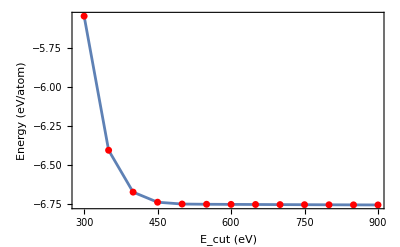

```mathematica
dataecut//ListPlot[#,
Frame->True,
FrameLabel->{"E_cut (eV)","Energy (eV/atom)" },
BaseStyle->{FontFamily -> "Helvetica", 
FontSize->18},
Joined->True,
PlotRange->All,
InterpolationOrder->1,
ImageSize->400,
Epilog->
{Red, AbsolutePointSize[5],
Point[#]}
]&
```

We  use meV precision because magnetic properties are really tiny. So we need this precision to describe these properties.

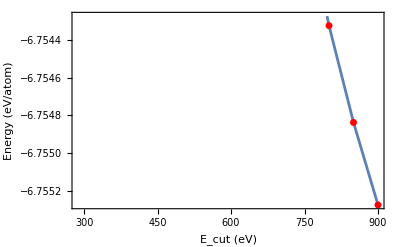

```mathematica
dataecut//ListPlot[#,
Frame->True,
FrameLabel->{"E_cut (eV)","Energy (eV/atom)" },
BaseStyle->{FontFamily -> "Helvetica", 
FontSize->18},
Joined->True,
PlotRange->{dataecut[[13,2]], dataecut[[13,2]]+ 10^-3},
InterpolationOrder->1,
ImageSize->400,
Epilog->
{Red, AbsolutePointSize[5],
Point[#]}
]&
```

We  use 800 eV for Cem from now on.

### Convergency of k-points

```mathematica
data = Import["kp.dat"]
```

{{1,-4660.48,43},{2,-4660.51,58},{3,-4660.51,37}}

```mathematica
kpdat =data[[All,{1,2}]]//Map[#/{1,690}&]
```

{{1,-6.75432},{2,-6.75437},{3,-6.75436}}

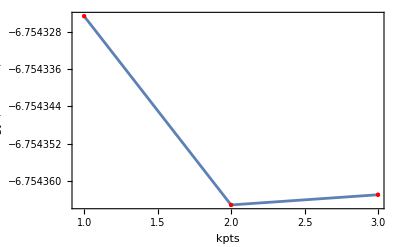

```mathematica
ListPlot[kpdat,
PlotRange->All,
Joined->True,
Mesh->Full,
MeshStyle->
{Directive[PointSize[Medium], Red]},
Frame->True,
FrameLabel->
{"kpts", "Energy (eV/atom)"},
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->18},
ImageSize->400]
```

Let’s analyse the convergency of these data using the 1 meV/atom criteria

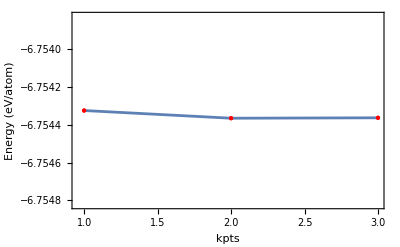

```mathematica
ListPlot[kpdat,
PlotRange->{kpdat[[1,2]]+10^-3/2, kpdat[[1,2]]-10^-3/2},
Joined->True,
Mesh->Full,
MeshStyle->
{Directive[PointSize[Medium], Red]},
Frame->True,
FrameLabel->
{"kpts", "Energy (eV/atom)"},
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->18},
ImageSize->400]
```

From this result, we use from now on the k-point grid 1x1x1